#### Mathematica file to compute New Physics contributions to g-2.

## 2HDM with a gauged U_(Lμ - L τ)symmetry Model.

Particles  Masses in GeV units.

```mathematica
mμ=0.105; (*Muon mass*)
mf:=mμ; 
ϵ:=1; (* ϵ:= mf/mμ*)
```

Experimental Bounds

based on:
		Current Bound: (261 ± 68) x 10^-11;
		Projected 1 sigma bound < 34 x 10^-11;

```mathematica
(*BoundCurrenteup=339*10^-11;
BoundCurrentdown=183*10^-11;
sigmaCurrent=78*10^-11;
sigmaProjected=34*10^-11;*)
```

```mathematica
up=420*10^-11;
down= 103*10^-11;
```

#### Z’ boson

L = gv Z' μ̄ γ^μ μ +  ga Z' μ̄ γ^μγ^5 μ  ~  gv Z' μ̄ γ^μ μ + 0.

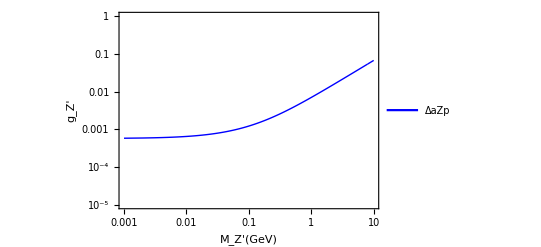

```mathematica
Pointsu={};
ΔaZpu=up;
Do[MZpu=0.001 (i-1)+0.001;gvu=√((ΔaZpu (8 π^2 MZpu^2))/(mμ^2 NIntegrate[(2 x (1-x) x)/((mμ/MZpu)^2 x+(1-x) (1-(mμ/MZpu)^2 x)),{x,0,1}]));AppendTo[Pointsu,{MZpu,gvu}],{i,10000}];
Export["C:\\Users\\yoxas\\OneDrive\\Documents\\PHD\\Pointsup.tsv",Pointsu];
ListLogLogPlot[{Pointsu},PlotStyle->{Directive[Blue,Thick]},Joined->True,PlotRange->{{1/10^3,10},{1/10^5,1}},Frame->True,FrameStyle->{{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]},{Directive[Black,12,Thickness[.005]],Directive[Black,12,Thickness[.005]]}},PlotTheme->"Scientific",PerformanceGoal->"Quality",FrameLabel->{Style[HoldForm[Subscript[M, Z'][GeV]],13,Black,Bold],Style[HoldForm[Subscript[g, Z']],16,Black,Bold]},PlotLegends->Placed[LineLegend[{"ΔaZp"}],{0.9,0.2}]]
```

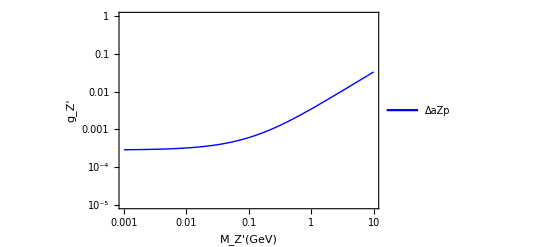

```mathematica
Pointsd = {};
ΔaZpd=down;
Do[MZpd = 0.001 + 0.001*(i-1);

gvd = Sqrt[((8* π^2*MZpd^2)*ΔaZpd)/(mμ^2* NIntegrate[(2*x*(1 - x)*(x))/((1 - x)*(1 - ((mμ/MZpd)^2*x)) +((mμ/MZpd)^2*x)) , {x,0, 1}])];
AppendTo[Pointsd,{MZpd,gvd}],{i,10000}];
Export["C:\\Users\\yoxas\\OneDrive\\Documents\\PHD\\Pointsdown.tsv",Pointsd];
ListLogLogPlot[{Pointsd}, PlotStyle -> {Directive[Blue, Thick]}, Joined -> True, PlotRange -> {{10^-3, 10}, {10^-5, 1}}, 
 Frame -> True,  FrameStyle -> {{Directive[Black, 12, Thickness[.005]],  Directive[Black, 12, Thickness[.005]]}, {Directive[Black, 12, 
     Thickness[.005]],  Directive[Black, 12, Thickness[.005]]}},   PlotTheme -> "Scientific", PerformanceGoal -> "Quality", 
 FrameLabel -> {Style[HoldForm[Subscript[M, Z'][GeV]], 13, Black, Bold], Style[HoldForm[Subscript[g, Z']], 16, Black, Bold]}, 
 PlotLegends ->   Placed[LineLegend[{"ΔaZp"}], {0.9, 0.2}]]
```

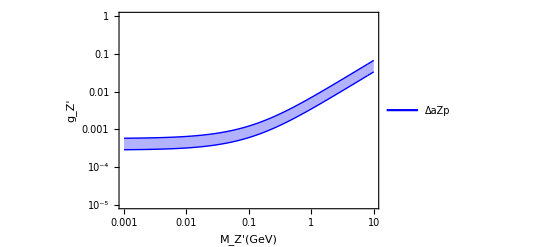

```mathematica
ListLogLogPlot[{Pointsu,Pointsd}, PlotStyle -> {Directive[Blue, Thick],Directive[Blue, Thick]}, Joined -> True, Filling->{1->{2}},PlotRange -> {{10^-3, 10}, {10^-5, 1}}, Frame -> True,  FrameStyle -> {{Directive[Black, 12, Thickness[.005]],  Directive[Black, 12, Thickness[.005]]}, {Directive[Black, 12, 
     Thickness[.005]],  Directive[Black, 12, Thickness[.005]]}},   PlotTheme -> "Scientific", PerformanceGoal -> "Quality", 
 FrameLabel -> {Style[HoldForm[Subscript[M, Z'][GeV]], 13, Black, Bold], Style[HoldForm[Subscript[g, Z']], 16, Black, Bold]}, 
 PlotLegends ->   Placed[LineLegend[{"ΔaZp"}], {0.9, 0.2}]]
```

```mathematica
(*FillingStyle->Directive[Opacity[0.5],Blue]*)
```

```mathematica
d1=Import["C:\\Users\\yoxas\\OneDrive\\Documents\\PHD\\2HDM_U1_Lmu_Ltau\\Datos\\Pointsup.tsv"];
d2=Import["C:\\Users\\yoxas\\OneDrive\\Documents\\PHD\\2HDM_U1_Lmu_Ltau\\Datos\\Pointsdown.tsv"];
(*Rest@Import*)

d3=Import["C:\\Users\\yoxas\\OneDrive\\Documents\\PHD\\2HDM_U1_Lmu_Ltau\\Datos\\BaBar4mu.dat", {"Data"}];
d4=Import["C:\\Users\\yoxas\\OneDrive\\Documents\\PHD\\2HDM_U1_Lmu_Ltau\\Datos\\BaBargamma.dat", {"Data"}];
d5=Import["C:\\Users\\yoxas\\OneDrive\\Documents\\PHD\\2HDM_U1_Lmu_Ltau\\Datos\\Borexino.dat", {"Data"}];
d6=Import["C:\\Users\\yoxas\\OneDrive\\Documents\\PHD\\2HDM_U1_Lmu_Ltau\\Datos\\Belle.dat", {"Data"}];
d7=Import["C:\\Users\\yoxas\\OneDrive\\Documents\\PHD\\2HDM_U1_Lmu_Ltau\\Datos\\CCFR.dat", {"Data"}];
```

Filling::invfillentry: {Top RGBColor[0.94, 0.88, 0.94]} is not a valid Filling specification.

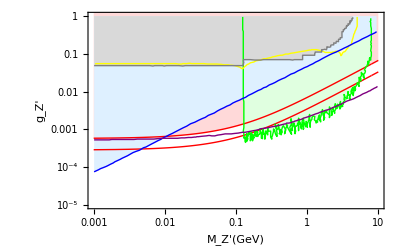

```mathematica
ListLogLogPlot[{d1,d2,d3,d4,d5,d6,d7}, PlotStyle -> {Directive[Red, Thick],Directive[Red, Thick],Directive[Green, Thick],Directive[Yellow, Thick],Directive[Blue, Thick],Directive[Gray, Thick],Directive[Purple, Thick]}, Joined -> True, Filling->{1->{2,LightRed},3->{Top, LightGreen}, 4-> {Top, LightYellow}, 5-> {Top,LightBlue}, 6-> {Top, LightGray}, 7->LightPurple{Top}},PlotRange -> {{10^-3, 10}, {10^-5, 1}},Frame -> True,  FrameStyle -> {{Directive[Black, 12, Thickness[.005]],  Directive[Black, 12, Thickness[.005]]}, {Directive[Black, 12, 
     Thickness[.005]],  Directive[Black, 12, Thickness[.005]]}},   PlotTheme -> "Scientific", PerformanceGoal -> "Quality", 
 FrameLabel -> {Style[HoldForm[Subscript[M, Z'][GeV]], 13, Black, Bold], Style[HoldForm[Subscript[g, Z']], 16, Black, Bold]}]
```